```mathematica
f=n
```

n

```mathematica
Table[f,{n,1,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
EvenQ[f]
```

False

```mathematica
EvenQ/@f
```

False

```mathematica
Table[EvenQ[p],{p,f}]
```

{True,False,False,False,False,False,False,False,False,False}

```mathematica
q=Table[n,{n,10}]
```

{0,1,2,2,3,3,4,4,4,4}

```mathematica
w=n
```

n

```mathematica
Table[w,{n,20}]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8}

```mathematica
Norm[{1,2,3}]
```

√14

```mathematica
Norm[{1,2,3,4,5,6,7,8,9,10}⟦1;;3⟧]
```

√14

```mathematica
Null
```

```mathematica
√(x^2+y^2+z^2)
```

√(x^2+y^2+z^2)

```mathematica
norm(x_,y_,z_):=√(x^2+y^2+z^2)
```

```mathematica
norm(1,2,3)
```

√14

```mathematica
normList1(v_):=√(v⟦1⟧^2+v⟦2⟧^2+v⟦3⟧^2)
```

```mathematica
normList1({1,2,3})
```

√14

```mathematica
normList2(v_):=norm@@v
```

```mathematica
Null
```

```mathematica
normList2({1,2,3})
```

√14

```mathematica
normRep(rep_):=√(x^2+y^2+z^2)/.rep
```

```mathematica
normRep({x->1,y->2,z->3})
```

√14

```mathematica
makePlot(data_,fn_):=Module[{listPlot,fnPlot,xMin,xMax},xMin=min(data⟦All,1⟧);xMax=max(data⟦All,1⟧);listPlot=ListPlot[data];fnPlot=Plot[fn(x),{x,xMin,xMax}];Return[Show[listPlot,fnPlot]];];
```

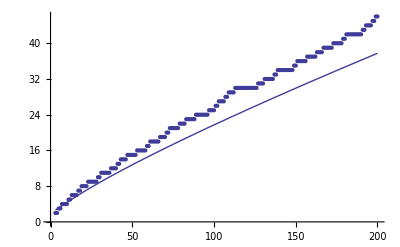

```mathematica
makePlot(Table[{n,n},{n,3,200}],#1/(log(#1))&)
```

```mathematica
Dominic Martinez-Ta
```

Dominic Martinez-Ta

```mathematica
Physics 132
```